-Graphics-

# Exploring Mathematica’s ML Algorithms

This notebook has been created with Mathematica Commercial License L3302-6545 .

June 25, 2020

Copyright (c) David M. Morgan
GNU General Public License, v. 3.0 or later

Antigonish Landing, NS B2G 2L2 Canada
david@dmmorganphd.ca; http://dmmorganphd.ca; (902) 318-4906

Problem:

Apply an appropriate ML algorithm to the discovery of a weak, noisy, sinusoidal dependence between two variables in an otherwise ten dimensional space in which all other variables vary randomly across 100 input vectors. Encode the relationship between variables 3 and 7. For starters, let’s use a moderate amount of noise. All other parameters vary between -1 and 1 uniformly randomly. 

Then, redo it so that the relationship is between the sum of variables 2 and 3.

Create 98 row vectors, each of which consists of 100 elements having values randomly distributed between 0 and 1.

```mathematica
bkgvectors = Table[ RandomReal[], {i, 100}, {j, 97}];
```

Create an additional vector of independent variable values for the relationship below.

```mathematica
indvector = Table[ RandomReal[], {i, 100}];
```

Create a dependent vector in which each element obeys the relationship:

0.5 + noise + 0.3 Sin[3 Pi indvector[[i]]]

```mathematica
depvector = Table[
0.5 + 0.2 Random[NormalDistribution[0,1]] +  0.3 Sin[3 Pi indvector[[i]]],
{i, 100}]
```

{0.666952,0.630998,0.0889395,0.314167,0.297965,0.540316,0.343398,0.314081,0.433313,0.882216,0.861693,0.317866,0.493951,0.677781,0.445053,1.11702,0.466896,0.329067,0.516182,0.901337,0.83071,0.741314,0.334503,-0.01845,0.533085,0.927979,0.817194,0.680997,0.320966,0.943062,0.803419,0.675606,0.646366,0.242375,0.172328,0.54147,0.660627,0.244707,0.906412,0.282889,0.217192,0.313684,0.625392,0.610239,0.70866,0.0343002,0.614102,0.736722,-0.0399216,1.01176,0.544667,0.353516,0.868183,0.511247,0.99434,0.969222,0.586456,0.321713,0.719817,0.498905,0.415598,0.0561859,0.623735,0.769394,0.822154,0.471045,0.684479,0.170971,0.126824,0.525773,0.611278,0.650953,0.458945,0.581832,0.564617,0.882193,0.607621,0.442004,0.536113,0.26576,0.847561,0.78946,0.928694,0.644534,0.0403034,0.670133,0.861043,0.388221,0.189568,0.162181,1.00132,0.390999,0.250613,0.705135,0.464109,0.612393,0.725538,0.355284,0.404396,0.889342}

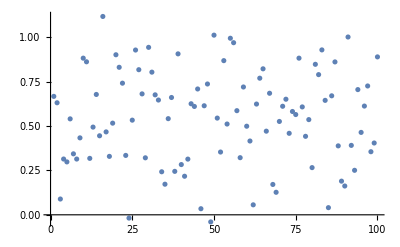

```mathematica
ListPlot[depvector]
```

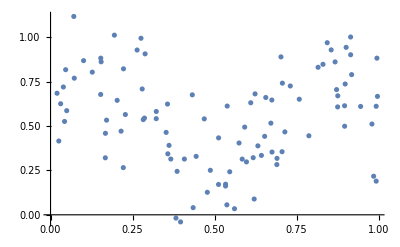

```mathematica
ListPlot[Transpose[{indvector, depvector}], PlotRange -> All]
```